Master Template for SNA Metrics
The colored font is what needs to change to ascertain different graph variables:

Example below is for ClosenessCentrality with suppressed output

```mathematica
topConnectedPersonsByCloseness=gleanWellConnectedPersons[#,"measure"->ClosenessCentrality]&/@accumulatingGraphs;
```

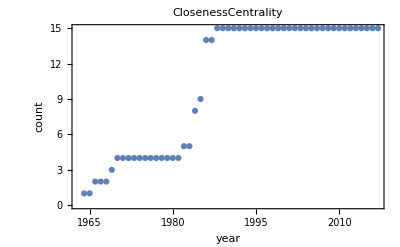

```mathematica
ListPlot[Length/@topConnectedPersonsByCloseness,FrameLabel->{"year","count"},Axes->False,Frame->True,PlotLabel->ClosenessCentrality]
```